# MSc Data Science - Introduction to Programming (PX 5007)

# Marco Thiel office: Meston Building 332 Email: m.thiel@abdn.ac.uk Twitter: @DataScienceUoA Office hours: Wednesday 1pm-2:00pm on Zoom Feedback link: https://wolfr.am/11JHosTl0 23 September 2025

## Assessments

These are the dates for the assessments:

Batch 1:

```mathematica
{{"First Assessment", DateObject[{2025,10,6},"Day"], "25% of mark.", "onsite computer assessement"}, {"Second Assessment", DateObject[{2025,10,13},"Day"], "25% of mark.", "onsite computer assessement"}, {"First Assessment", DateObject[{2025,10,27},"Day"], "50% of mark.", "onsite computer assessement"}}
```

```mathematica
{{"First Assessment", DateObject[{2025,10,6},"Day"], "25% of mark.", "online assessement - open until end of Monday"}, {"Second Assessment", DateObject[{2025,10,13},"Day"], "25% of mark.", "online assessement - open until end of Monday"}, {"First Assessment", DateObject[{2025,10,27},"Day"], "50% of mark.", "online assessement - open until end of Friday"}}
```

Batch 2 (part time only)

```mathematica
{{"First Assessment", DateObject[{2025,11,7},"Day"], "25% of mark.", "online assessement open until end of Thursday"}, {"Second Assessment", DateObject[{2025,11,21},"Day"], "25% of mark.", "online assessement open until end of Thursday"}, {"First Assessment", DateObject[{2025,12,5},"Day"], "50% of mark.", "online assessement open until end of Thursday"}}
```

## Why you shouldn’t think of the Wolfram Language as a Programming Language

In many aspects the Wolfram Language is more similar to a natural language than to a programming language:

```mathematica
Grid[Map[Style[#,FontFamily->"Roboto",20]&,{
{"","Natural Language","Wolfram Language","Programming Language"},{"number of \"words\"","approx "<>ToString[Length[DeleteDuplicates[WordStem[ToLowerCase[TextWords[ExampleData[{"Text","AliceInWonderland"}]]]]]]]<>" to "<>ToString[Length[DeleteDuplicates[WordStem[WordList[]]]]],"Functions: "<>ToString[Length[Drop[Names["System`*"],116]]] ,"Key words in C++: "<>ToString[Length[Flatten[Import["https://en.cppreference.com/w/cpp/keyword","Data"][[2,1,-1,1]]]]]},
{"provenance","evolved naturally","designed","designed"},{"meaning context dependent","yes","yes","no"},{"multi level","yes","yes","no"},{"alternative expressions","very large","large","small"},{"ambiguity","yes","deals with ambiguity","no"},{"abstraction of domain","low","low","high"}},{2}],
Frame->All,Background->{None,None,{{1,1}->LightBlue,{1,2}->LightBlue,{1,3}->LightBlue,{1,4}->LightBlue,{2,1}->LightBlue,{3,1}->LightBlue,{4,1}->LightBlue,{5,1}->LightBlue,{6,1}->LightBlue,{7,1}->LightBlue,{8,1}->LightBlue}}]
```

| Natural Language | Wolfram Language | Programming Language
number of "words" | approx 1301 to 27261 | Functions: 6639 | Key words in C++: 92
provenance | evolved naturally | designed | designed
meaning context dependent | yes | yes | no
multi level | yes | yes | no
alternative expressions | very large | large | small
ambiguity | yes | deals with ambiguity | no
abstraction of domain | low | low | high

## Meaning Context Dependent

Functions can give different values depending on your context:

```mathematica
Sunset[]
```

Minute: Mon 29 Jun 2020 22:08GMT+1.

```mathematica
GeoDistance[Here, Entity["City",{"Champaign","Illinois","UnitedStates"}]]
```

3823.21 mi

Functions “can do different things” depending on their input:

```mathematica
2^2
```

4

```mathematica
ExampleData[{"TestImage","Couple"}]^2
```

-Graphics-

## Multi Level

### Natural language input vs coding

plot sin function in red on gray background

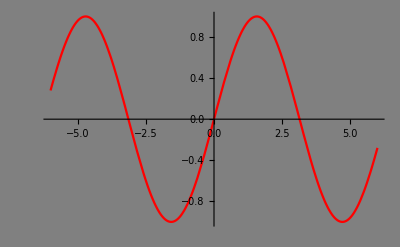

```mathematica
Plot[Sin[x], {x, -6., 6.}, PlotStyle -> Red, Background -> Gray, Evaluated -> True]
```

### Natural language input vs coding

Classifier without help:

```mathematica
cl=Classify[ExampleData[{"MachineLearning","Titanic"},"Data"],PerformanceGoal->"Quality"]
```

ClassifierFunction[…]

Classifier with prescribed method:

```mathematica
cl2=Classify[ExampleData[{"MachineLearning","Titanic"},"Data"],Method->"NearestNeighbors",PerformanceGoal->"Quality"]
```

ClassifierFunction[…]

Classifier based on neural network:

```mathematica
clnnet=Classify[ExampleData[{"MachineLearning","Titanic"},"Data"],Method->"NeuralNetwork",PerformanceGoal->"Quality"]
```

ClassifierFunction[…]

```mathematica
net=(First@clnnet)["Model"]["Network"]
```

NetChain[<>]

```mathematica
cl[{"1st",37,"male"}]
```

died

```mathematica
cl2[{"1st",37,"male"}]
```

died

```mathematica
clnnet[{"1st",37,"male"}]
```

died

## Alternative expressions

Procedural programming:

```mathematica
result={1,1};Do[AppendTo[result,Total[Take[result,-2]]],{i,1,10}];result
```

{1,1,2,3,5,8,13,21,34,55,89,144}

```mathematica
result2={1,1};For[i=2,i≤11,i++,AppendTo[result2,Total[result2[[i-1;;i]]]]];result2
```

{1,1,2,3,5,8,13,21,34,55,89,144}

Via definition of a function:

```mathematica
Clear[f];
f[1]=1;
f[2]=1;
f[n_]:=f[n]=f[n-1]+f[n-2]
```

```mathematica
Table[f[k],{k,1,12}]
```

{1,1,2,3,5,8,13,21,34,55,89,144}

Using nested, built-in functions:

```mathematica
Fibonacci[Range[12]]
```

{1,1,2,3,5,8,13,21,34,55,89,144}

or

```mathematica
Nest[Join[#,{Total[Take[#,-2]]}]&,{1,1},10]
```

{1,1,2,3,5,8,13,21,34,55,89,144}

Rule based programming:

```mathematica
Quiet[ReplaceRepeated[{1,1},{a___,x_,y_}->{a,x,y,x+y},MaxIterations->10]]
```

{1,1,2,3,5,8,13,21,34,55,89,144}

## Ambiguity

```mathematica
SemanticInterpretation["congo", AmbiguityFunction->All]
```

AmbiguityList[{Democratic Republic of the Congo,Republic of the Congo,San Salvador Kongo,Koongo,Congo River,Congo,congo}]

```mathematica
SemanticInterpretation["sun", AmbiguityFunction->All]
```

AmbiguityList[{Sun,Day: Sun 5 Jul 2020,sun,Sun}]

## Abstraction of domain (“how real are the concepts”)

Distance between two cities (distances between different entities):

```mathematica
GeoDistance[Entity["City",{"Champaign","Illinois","UnitedStates"}]["Coordinates"],Entity["City",{"Chicago","Illinois","UnitedStates"}]["Coordinates"]]
```

122.824 mi

```mathematica
GeoDistance[Entity["City",{"Champaign","Illinois","UnitedStates"}]["Polygon"],Entity["City",{"Chicago","Illinois","UnitedStates"}]["Polygon"]]
```

106.967 mi

Obviously, we need to specify whether we mean the distances between the centres of the cities or the distance between the borders of the cities.

Different types of distances:

There are different travel methods. They will also lead to different results.

```mathematica
GeoDistance[Entity["City",{"London","GreaterLondon","UnitedKingdom"}], Entity["City",{"Aberdeen","AberdeenCity","UnitedKingdom"}]]
```

397.754 mi

```mathematica
TravelDistance[{Entity["City",{"London","GreaterLondon","UnitedKingdom"}], Entity["City",{"Aberdeen","AberdeenCity","UnitedKingdom"}]}]
```

518.309 mi

```mathematica
TravelDistance[{Entity["City",{"London","GreaterLondon","UnitedKingdom"}], Entity["City",{"Aberdeen","AberdeenCity","UnitedKingdom"}]},TravelMethod->"Walking"]
```

784.653 mi

```mathematica
GeoLength[GeoPath[{Entity["City",{"London","GreaterLondon","UnitedKingdom"}], Entity["City",{"Aberdeen","AberdeenCity","UnitedKingdom"}]},"RhumbLine"]]
```

397.767 mi

```mathematica
TravelDirections [{Entity["City",{"London","GreaterLondon","UnitedKingdom"}], Entity["City",{"Aberdeen","AberdeenCity","UnitedKingdom"}]},TravelMethod->"Walking"]
```

TravelDirectionsData[…]

```mathematica
GeoGraphics[Style[Line[%],Thick,Red]]
```

## Complexity of the Wolfram Language - how to find your way around...

We have seen that the Wolfram Language has basically as many functions as we have words in a spoken language. That means that it is difficult to teach the language in few hours. This makes the Wolfram Language very efficient, but also requires speakers to learn a large vocabulary.

Mathematica has many more functions/commands than low level languages like C/C++. This can make coding much more efficient. Here is a comparison based on code from the Rosetta Code Project.

Let’s first compare the line count in several languages (for a more comprehensive comparison see here):

This graph shows a comparison of all code C vs MMA:

This, for example, would be quite a substantial piece of code in C:

```mathematica
Dynamic[i=CurrentImage[];boxes=FindFaces[i];
HighlightImage[i,Rectangle@@@boxes]]
```

```mathematica
DeviceClose/@Devices[];
```

### So, which functions are there?

```mathematica
Names["System`*"]
```

```mathematica
Names["System`*"]//Length
```

```mathematica
RandomChoice[Names["System`*"],10]
```

```mathematica
WolframLanguageData["Cos","RelationshipCommunityGraph"]
```

-Graphics-

```mathematica
(funData=WolframLanguageData["Sin","PropertyAssociation"])//Short
```

<|attributes→{Listable,NumericFunction,Protected},character count→3,common option values→Missing[NotApplicable],date introduced→Day: Thu 23 Jun 1988,«41»,version introduced→1,version last modified→10.1,versions modified→{4,10,10.1},Wolfram documentation link→Sinpaclet:ref/Sin|>

```mathematica
With[{props=SortBy[Normal[funData],LeafCount]},
Manipulate[property/.props,{{property,EntityProperty["WolframLanguageSymbol","RelationshipCommunityGraph"]},props[[All,1]]},SaveDefinitions->True]
]
```

### A test question

## Computation using a high level language: Mathematica

Mathematica is part of Siri:

How many atoms are there in the Universe

weather in Aberdeen

weight of an elephant

molecular structure of coffein

compare  mount everest vs ben nevis

satellites overhead

plot sine function with gray background in yellow

```mathematica
images={-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ImageIdentify[#]&/@ images
```

### Ending oversimplification - speaking about reality

```mathematica
cow=ExampleData[{"Geometry3D","Cow"}];
Manipulate[ImageResize[cow/.GraphicsComplex[array1_,rest___]:>GraphicsComplex[(# (Norm[#]^-coeff))&/@array1,rest],400],{{coeff,0.,"sphericity"},0,1}]
```

ImageResize::imginv: Expecting an image or graphics instead of cow.

```mathematica
cow=ExampleData[{"Geometry3D","Cow"}]
```

```mathematica
DiscretizeGraphics[cow]
```

```mathematica
NIntegrate[1,{x,y,z}∈DiscretizeGraphics[cow]]
```

```mathematica
(*comet=Import["http://sci.esa.int/science-e/www/object/doc.cfm?fobjectid=54726","OBJ"];*)
comet=Import["ESA_Rosetta_OSIRIS_67P_SHAP2P.obj","Graphics3D"]
```

### Question

## The Wolfram Language contains many advanced algorithms

There are many rather complicated algorithms that are built right into the Wolfram Language:

```mathematica
europe=CountryData["Europe"];
pos= GeoPosition[CountryData[#,"CapitalLocation"]]&/@ europe;
{albania,spain}=Flatten[Position[europe,#]&/@{Entity["Country","Albania"],Entity["Country","Spain"]}];
```

```mathematica
tour=FindShortestTour[pos, albania, spain]
```

Show the tour:

```mathematica
GeoGraphics[{Thick, Red,GeoPath[europe[[tour[[2]]]]]},ImageSize->Large]
```

-Graphics-

This gives the shortest round tour though the centres of all countries world-wide.

```mathematica
places=CountryData["Countries"];
centers=Map[GeoPosition[CountryData[#,"CenterCoordinates"]]&,places];
{dist,route}=FindShortestTour[centers];
```

```mathematica
GeoGraphics[{Thick,GeoPath[centers[[route]]]},GeoRange->"World",ImageSize->Large]
```

-Graphics-

This can earn you a lot of money (drill tool). Suppose you need to drill holes in a circuit board. If you move the drill optimally you will save time (and money).

```mathematica
{{-Graphics-, -Graphics-}}
```

80% of the tool travel has been eliminated, therefore more can be produced on the same machine.

Let’s take some images from the BBC website:

```mathematica
imagesBBC=Select[Import["http://www.bbc.co.uk/news","Images"],(ImageQ[#]&&ByteCount[#]>400)&]
```

```mathematica
ImagePartition[imagesBBC[[2]],12]
```

```mathematica
DominantColors[imagesBBC[[2]]]
```

We can also import all the text from the BBC news website:

```mathematica
WebImage["http://www.bbc.co.uk/news"]
```

```mathematica
textBBC=Import["http://www.bbc.co.uk/news","Plaintext"]
```

## Machine Learning

### Day and night classifier

```mathematica
trainingsdataset={-Graphics--> "Day",-Graphics--> "Day",-Graphics--> "Day",-Graphics--> "Day",-Graphics--> "Day",-Graphics--> "Day",-Graphics-->"Day",-Graphics--> "Night", -Graphics--> "Night", -Graphics--> "Night", -Graphics--> "Night"}
```

```mathematica
cdaynight=Classify[trainingsdataset]
```

ClassifierFunction[…]

```mathematica
testset={-Graphics-,-Graphics-}
```

```mathematica
cdaynight[#]&/@ testset
```

{Night,Day}

### Titanic

We use data from the survival of the Titanic disaster to predict survival rates.

```mathematica
dataset=ExampleData[{"MachineLearning","Titanic"},"Data"];
c=Classify[dataset,Method->"LogisticRegression"]
```

ClassifierFunction[…]

```mathematica
c[{"2nd",37,"male"},{"Probability","survived"}]
```

0.0530765

```mathematica
p[class_,age_,sex_]:=c[{class,age,sex},{"Probability","survived"}];
Plot[{p["1st",x,"female"],p["3rd",x,"female"],p["1st",x,"male"],p["3rd",x,"male"]},{x,0,100},PlotLegends->{"female, 1st class","female, 3rd class","male, 1st class","male, 3rd class"},Frame->True,FrameLabel->{"Age (years)","Survival probability"}]
```

### Recognise what images show

```mathematica
imgElephant=CloudGet["https://wolfr.am/L9qz1zu4"]
```

-Graphics-

```mathematica
ImageBoundingBoxes[imgElephant]
```

<|elephant→{Rectangle[{433.923,102.865},{553.362,211.964}],Rectangle[{336.372,155.731},{474.614,272.098}],Rectangle[{160.801,107.681},{409.561,262.771}]},zebra→{Rectangle[{35.9317,19.1565},{206.023,159.265}],Rectangle[{3.46491,152.314},{78.4044,211.948}],Rectangle[{133.182,94.3629},{223.032,172.756}]}|>

```mathematica
HighlightImage[imgElephant,%]
```

-Graphics-

## Automatic theorem proving

Mathematica has an advanced automatic proof system built in:

```mathematica
proofSocrates=FindEquationalProof[mortal[socrates],{ForAll[x,Implies[man[x],mortal[x]]],man[socrates]}]
```

```mathematica
proofSocrates["ProofGraph"]
```

### More relevant examples (a proof in group theory)

AxiomaticTheory provides a collection of standard axiom systems. One of them is an axiom system for group theory:

```mathematica
axioms=AxiomaticTheory[{"GroupAxioms","Multiplication"->p,"Identity"->e}]
```

{∀_{a,b,c}p[a,p[b,c]]==p[p[a,b],c],∀_a p[a,e]==a,∀_a p[a,ā]==e}

This axiom system is sufficient to allow proofs of general results about groups. For example, we can show that—even though the axioms only asserted that e is a right identity—it is possible to prove from the axioms that it is also a left identity:

```mathematica
FindEquationalProof[p[e,x]==x,axioms]
```

```mathematica
Dataset[%["ProofDataset"],MaxItems->{6,1}]
```

### The Quaternion group

But if you want to prove a result not about groups in general, but about a specific finite group, then you need to add to the axioms the particular defining relations for your group. You can get these from FiniteGroupData. Here are the axioms for the quaternion group, given in a default notation:

```mathematica
FiniteGroupData["Quaternion","DefiningRelations"]
```

To use these axioms in FindEquationalProof, we need to merge their notation with the notation we use for the underlying group axioms. In Version 12.1, you can do this directly in AxiomaticTheory:

```mathematica
AxiomaticTheory[{"GroupAxioms","Quaternion","Multiplication"->p,"Identity"->e}]
```

But to use the most common notation for quaternions, we have to specify a little more:

```mathematica
AxiomaticTheory[{"GroupAxioms","Quaternion",<|"Multiplication"->p,"Inverse"->inv,"Identity"->e,"Generators"->{i,j}|>}]
```

{∀_{a,b,c}p[a,p[b,c]]==p[p[a,b],c],∀_a p[a,e]==a,∀_a p[a,inv[a]]==e,p[p[i,j],i]==j,p[p[j,i],j]==i}

But now we can prove theorems about the quaternions. This generates a 54-step proof that the 4th power of the generator we have called i is the identity:

```mathematica
FindEquationalProof[p[i,p[i,p[i,i]]]==e,%]
```

ProofObject[…]

## Main structures in the Wolfram Language

There are classes of objects in the Wolfram Language that are particularly important. The idea is that you have objects that you want to work with (numbers, images, sound etc). Then you manipulate them, i.e. you apply some sort of function to them. Oftentimes, you want to operate on collections of things. That is - in a nutshell- what the following objects allow you to do.

### Expressions

There are different types of objects in the Wolfram Language. Here are some basic ones:

#### Numbers

Integers (infinite precision, no decimal point):

```mathematica
1,2,3
```

Rationals (fractions, infinite precision, no decimal points)

```mathematica
1/2,7/11,9/3
```

Reals (finite precision, decimal point)

```mathematica
0.5,0.78, 0.111
```

Note that this is not quite the same notation as you might be used to in maths. We can for example have infinite precision real numbers in the Wolfram Language:

```mathematica
Pi,Sqrt[2]
```

Complex numbers (infinite or finite precision)

```mathematica
1+2I, 1.-3.I,3I
```

#### Images

We can work with images:

```mathematica
ExampleData[{"TestImage","Apples"}]
```

or even 3D images:

```mathematica
ExampleData[{"TestImage3D","MRknee"}]
```

#### Sound

Sound objects can be imported, manipulated and exported:

```mathematica
a=ExampleData[{"Sound","Apollo11SmallStep"},"Audio"]
```

Then you can directly work with these objects:

```mathematica
WienerFilter[a,25]
```

You can even compose music:

```mathematica
freude={{"E",.5},{"E",.5},{"F",.5},{"G",.5},{"G",.5},{"F",.5},{"E",.5},{"D",.5},{"C",.5},{"C",.5},{"D",.5},{"E",.5},{"E",.75},{"D",.25},{"D",1}};
```

We can play that on an organ

```mathematica
Sound[SoundNote[#1,#2,"Organ"] & @@@ freude]
```

or a piano

```mathematica
Sound[SoundNote[#1,#2,"Piano"] & @@@ freude]
```

#### Videos

Videos can are just another one of the objects we can work on:

```mathematica
v=Video["ExampleData/bullfinch.mkv",Appearance->"Basic"]
```

The next line will find the finch on the video (run-time too long for lecture):

```mathematica
(*VideoFrameMap[HighlightImage[#,ImageBoundingBoxes[#]]&,v]*)
```

Here is the result:

```mathematica
Video[Import["findthefinch.mkv"],Appearance->"Basic"]
```

#### Entities

Another object we can operate on are Entities (you can type them in using control + =.

```mathematica
LinguisticAssistant
```

Here are some examples:

```mathematica
Entity["City",{"Aberdeen","AberdeenCity","UnitedKingdom"}]
```

```mathematica
GeoGraphics[%]
```

```mathematica
Entity["AnatomicalStructure","RightHand"]
```

```mathematica
AnatomyPlot3D[Entity["AnatomicalStructure","RightHand"]]
```

```mathematica
Entity["Chemical","Caffeine"]
```

```mathematica
MoleculePlot3D[Entity["Chemical","Caffeine"]]
```

#### EntityLists

Some objects contain a list of entities:

```mathematica
LinguisticAssistant
```

```mathematica
EntityList[LinguisticAssistant]
```

#### ProofObjects

There are proof objects:

```mathematica
proofSocrates=FindEquationalProof[mortal[socrates],{ForAll[x,Implies[man[x],mortal[x]]],man[socrates]}]
```

ProofObject[…]

WHich can then be analysed:

```mathematica
proofSocrates["ProofGraph"]
```

#### FittedModels

We can also use curve fitting and obtain a model:

```mathematica
dataFibonacci= Fibonacci[Range[13]];
```

```mathematica
lm=LinearModelFit[dataFibonacci,{1,x,x^2,x^3,x^4},x]
```

FittedModel[«6»+0.0437491 x^4]

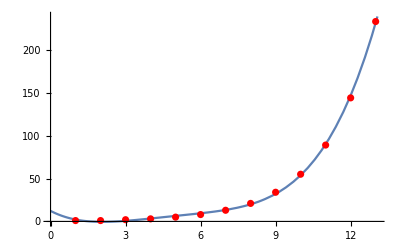

```mathematica
Show[Plot[lm[x],{x,0,14}],ListPlot[dataFibonacci,PlotStyle->Red],PlotRange->All]
```

```mathematica
lm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 12.2727 | 4.46595 | 2.74806 | 0.025134
x | -15.1283 | 4.06188 | -3.72445 | 0.00583398
x^2 | 5.84313 | 1.12111 | 5.2119 | 0.000810552
x^3 | -0.828997 | 0.118273 | -7.00919 | 0.000111611
x^4 | 0.0437491 | 0.0041981 | 10.4212 | 6.23296×10^-6

#### Datasets

```mathematica
ds=ExampleData[{"Dataset","Planets"}]
```

```mathematica
ds["Jupiter","Mass"]/ds[Total,"Mass"]
```

0.71158

#### Associations

The structure that underlies a dataset is an association:

```mathematica
ds//Normal
```

#### Functions

see below

### Lists (of expressions)

Sometimes you might want to group objects into an ordered list:

```mathematica
number=Range[5]
```

{1,2,3,4,5}

```mathematica
word=RandomWord[5]
```

{laxly,idle,coercion,oddity,highlight}

```mathematica
webImages=WebImageSearch["Tiger"]
```

You can combine objects of different types of objects

```mathematica
Manipulate[Plot[Sin[a x],{x,-6,6}],{a,1,5}]
```

```mathematica
list={1, 3.5, Sqrt[2],-Graphics-,-Graphics-,-Graphics3D-,}
```

You can access elements of lists with the Part function

```mathematica
Part[list,2]
```

3.5

Or short

```mathematica
list[[2]]
```

3.5

You can access a range:

```mathematica
list[[1;;5]]
```

or advance “in steps of”:

```mathematica
list[[1;;6;;2]]
```

List of lists are “matrices”

```mathematica
mat=RandomInteger[10,{3,3}]
```

{{4,6,2},{4,10,6},{3,8,1}}

```mathematica
mat//MatrixForm
```

(4 | 6 | 2
4 | 10 | 6
3 | 8 | 1)

You can access the second column like so:

```mathematica
mat[[All,2]]
```

{6,10,8}

and the second row like so:

```mathematica
mat[[2]]
```

{4,10,6}

The function TreeForm can help to find your way around:

```mathematica
TreeForm[mat]
```

### Functions

#### Functions on different domains

Operate on these objects using functions:

```mathematica
Sin[4.]
```

-0.756802

We have to observe that by default we do not waste precision:

```mathematica
Sin[4]
```

Sin[4]

This is hugely important (sorry for using a “pure function”):

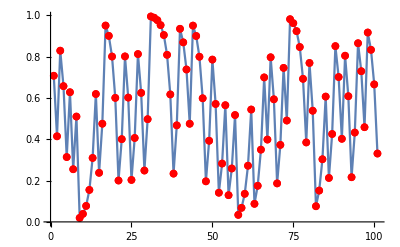

```mathematica
ListLinePlot[NestList[Mod[2#,1]&,1/Sqrt[2],100],Mesh->Full,MeshStyle->Red]
```

```mathematica
ColorNegate[webImages[[1]]]
```

We can nest these functions

```mathematica
CurrentImage[]
```

There are modifiers that you can use:

```mathematica
Plot[Sin[x],{x,-6,6}]
```

vs

```mathematica
Plot[Sin[x],{x,-6,6},PlotTheme->"Marketing"]
```

You can also use interactive components:

```mathematica
Manipulate[Plot[b h[c x],{x,-6,6},PlotRange->{All,{-4,4}}],{h,{Sin,Tan,Cos}},{b,0,4},{c,1,4}]
```

#### Define your own function

We can easily define our own functions:

```mathematica
f[x_]:= Sin[x]^2+6
```

```mathematica
f[9.7]
```

We can restrict the domain of a function

```mathematica
isFour[4]:="Yes!!";
isFour[x_Integer]:="No, but "<>ToString[x]<>" is an integer!";
isFour[x_?NumericQ]:="No, but "<>ToString[x]<>" is a number.";
isFour[_]:="No, not even close to four...";
```

Note the := symbol (set-delayed); we can compare that to the standard “set”

```mathematica
rand=RandomReal[]
```

0.143095

```mathematica
rand2:=RandomReal[]
```

```mathematica
Table[rand,10]
```

{0.143095,0.143095,0.143095,0.143095,0.143095,0.143095,0.143095,0.143095,0.143095,0.143095}

```mathematica
Table[rand2,10]
```

{0.959468,0.404997,0.703824,0.820619,0.760119,0.552566,0.650094,0.391922,0.386629,0.409657}

#### Pure functions

Pure functions are a very powerful concept in the Wolfram Language. Suppose we have the function from above:

```mathematica
f[x_]:= Sin[x]^2+6
```

To convert that into a pure function, i.e. a function with no name and without named input variables, we will:

(1) only take the right hand side:

```mathematica
Sin[x]^2+6
```

(2) substitute the variable by the slot symbols #:

```mathematica
Sin[#]^2+6
```

(3) Finish the function off with an &

```mathematica
Sin[#]^2+6&
```

This construct acts like a standard function:

```mathematica
Sin[#]^2+6&[3.6]
```

## Basic rules of the Wolfram Language

The name of a function or command in the Wolfram language is an Expression.  The structure of an expression is this:

Head[argument1, argument2 ...]

The three main features of an expression:

The Head.

The head is the name of the expression (for example Integrate), and usually describes what the function does.  All the words are capitalised, a format called CamelCase.

Square brackets.

All expressions use square brackets straight after the head.

Comma separated arguments.

Put the arguments inside the square brackets, and separate them with commas.

The final part of an expression is how to evaluate it!  Unlike the Wolfram Alpha query, you must press ⇧⌤ to evaluate the cell.

## Functional Programming

Functional programming is (my) preferred style of programming. The basic idea is that you wrap functions around each other.

```mathematica
CurrentImage[]
```

You can also use “pre-fix” notation for this:

```mathematica
Dynamic@ColorNegate@EdgeDetect@CurrentImage[]
```

Or alternatively, the “post-fix”

```mathematica
CurrentImage[]//EdgeDetect//ColorNegate//Dynamic
```

### Useful functions for functional programming:

#### Map

We can map a function over a list of objects:

```mathematica
Map[g,Range[5]]
```

{g[1],g[2],g[3],g[4],g[5]}

This can be done in a short-hand form like this:

```mathematica
g/@Range[5]
```

{g[1],g[2],g[3],g[4],g[5]}

This can help to not use a loop structure:

```mathematica
For[i=1,i≤5,i++,Print[g[i]]]
```

#### Thread

Thread[f[args]] threads a function f over lists that appear in the provided argument.

```mathematica
Thread[f[{a,b,c},{1,2,3}]]
```

{f[a,1],f[b,2],f[c,3]}

```mathematica
Rule@@@Transpose[{{"class","age","sex"},{"1st",32,"female"}}]
```

{class→1st,age→32,sex→female}

```mathematica
Thread[Rule[{"class","age","sex"},{"1st",32,"female"}]]
```

{class→1st,age→32,sex→female}

```mathematica
MatrixForm[{{"class","age","sex"},{"1st",32,"female"}}]
```

(class | age | sex
1st | 32 | female)

```mathematica
MatrixForm[Transpose[{{"class","age","sex"},{"1st",32,"female"}}]]
```

(class | 1st
age | 32
sex | female)

```mathematica
Thread[{a,b,c}->{1,2,3}]
```

{a→1,b→2,c→3}

```mathematica
Thread[{{a,b,c},{1,2,3}}]
```

{{a,1},{b,2},{c,3}}

Thread requires all arguments to be of equal length or single elements.

```mathematica
Thread[{{a,b,c},AA,{1,2,3}}]
```

{{a,AA,1},{b,AA,2},{c,AA,3}}

#### Apply

Apply replaces the head of the expression to which it is applied. It uses the form Apply[f, expr]. You could also use @@, which is the shorthand form.

```mathematica
Apply[g,f[a,b,c]]
g@@f[a,b,c]
```

g[a,b,c]

g[a,b,c]

```mathematica
Apply[Plus,{1,2,3}]
```

6

```mathematica
Plus[1,2,3]
```

6

The head of an expression can be obtained by using the function Head.

```mathematica
Head[{a,b,c,d,e}]
```

Change the head from List to Times by using Apply.

```mathematica
Apply[Times,{a,b,c,d,e}]
```

#### Fold

Another function that can help us to avoid loops is:

```mathematica
v=.;a=.
```

```mathematica
Fold[v,x,{a,b,c,d}]
```

v[v[v[v[x,a],b],c],d]

```mathematica
Fold[1/(#2+#1)&,x,Reverse[{a,b,c,d}]]
```

## One last tip before we start

You have seen now some of the fundamental constructs in the Wolfram Language. There are many more (Sow, Reap, Catch, Throw, MapThread, ...) 
It is quite impossible to discuss all the functions in one presentation or even a week of presentations. So how do you find the function you need?

As “all” the functions are plain English, you can just start to type:

The best resources are in the extensive documentation:

Learn how to work with the documentation of individual functions:

```mathematica
Plot
```

Use built-in functions if you can.

Search before you implement your own functions.

## Some programming tasks

Simulate a three body problem in 2D using NBodySimulation.

Extend the program to 3D.

Build a classifier for limes and lemons using Classify. Take images from the internet using WebImageSearch.

Use Classify to find a “notable person” that looks like you.

Use FacialFeatures to get an estimate of your age, sex and “emotional state”.

Use WeatherData to obtain Windspeed data for your current location; you will obtain a time series. Then plot it using DateListPlot. Use QuantityMagnitude to strip off the units. The use FindDistribution to estimate the distribution of the data.

Find different ways of computing the prime numbers below 100.

Use ListPlot to plot a sin function from -6 to 6 evaluated at steps of 0.1.

Use an appropriate network from the Wolfram Function Repository to color this image:

```mathematica
ExampleData[{"TestImage","Couple2"}]
```

Use FindTextualAnswer and WikipediaData to find out what the horn of a rhino is made of, without reading the article.

Spot the difference

```mathematica
{img1=-Graphics-,img2=-Graphics-}
```

## Function dictionary for this file

```mathematica
{{"NotebookDirectory"paclet:ref/NotebookDirectory, "FileNameJoin"paclet:ref/FileNameJoin, "SetDirectory"paclet:ref/SetDirectory, "Reverse"paclet:ref/Reverse, "Fold"paclet:ref/Fold}, {"Unset"paclet:ref/Unset, "Head"paclet:ref/Head, "Transpose"paclet:ref/Transpose, "Thread"paclet:ref/Thread, "Print"paclet:ref/Print}, {"EdgeDetect"paclet:ref/EdgeDetect, "RandomReal"paclet:ref/RandomReal, "NumericQ"paclet:ref/NumericQ, "PatternTest"paclet:ref/PatternTest, "Integer"paclet:ref/Integer}, {"Cos"paclet:ref/Cos, "Tan"paclet:ref/Tan, "PlotTheme"paclet:ref/PlotTheme, "ColorNegate"paclet:ref/ColorNegate, "MeshStyle"paclet:ref/MeshStyle}, {"Full"paclet:ref/Full, "Mesh"paclet:ref/Mesh, "Mod"paclet:ref/Mod, "NestList"paclet:ref/NestList, "ListLinePlot"paclet:ref/ListLinePlot}, {"TreeForm"paclet:ref/TreeForm, "MatrixForm"paclet:ref/MatrixForm, "RandomInteger"paclet:ref/RandomInteger, "ViewVertical"paclet:ref/ViewVertical, "ViewPoint"paclet:ref/ViewPoint}, {"ViewAngle"paclet:ref/ViewAngle, "SphericalRegion"paclet:ref/SphericalRegion, "Keys"paclet:ref/Keys, "FreeQ"paclet:ref/FreeQ, "Not"paclet:ref/Not}, {"Condition"paclet:ref/Condition, "False"paclet:ref/False, "Boxed"paclet:ref/Boxed, "ImageScaled"paclet:ref/ImageScaled, "Lighting"paclet:ref/Lighting}, {"TooltipStyle"paclet:ref/TooltipStyle, "VertexNormals"paclet:ref/VertexNormals, "Polygon"paclet:ref/Polygon, "Annotation"paclet:ref/Annotation, "Tooltip"paclet:ref/Tooltip}, {"Specularity"paclet:ref/Specularity, "EdgeForm"paclet:ref/EdgeForm, "Graphics3D"paclet:ref/Graphics3D, "SampledSoundList"paclet:ref/SampledSoundList, "MetaInformation"paclet:ref/MetaInformation}, {"Sqrt"paclet:ref/Sqrt, "WebImageSearch"paclet:ref/WebImageSearch, "RandomWord"paclet:ref/RandomWord, "PlotRange"paclet:ref/PlotRange, "ListPlot"paclet:ref/ListPlot}, {"Show"paclet:ref/Show, "LinearModelFit"paclet:ref/LinearModelFit, "EntityList"paclet:ref/EntityList, "EntityClass"paclet:ref/EntityClass, "MoleculePlot3D"paclet:ref/MoleculePlot3D}, {"AnatomyPlot3D"paclet:ref/AnatomyPlot3D, "Failure"paclet:ref/Failure, "Appearance"paclet:ref/Appearance, "Video"paclet:ref/Video, "SoundNote"paclet:ref/SoundNote}, {"Sound"paclet:ref/Sound, "WienerFilter"paclet:ref/WienerFilter, "Association"paclet:ref/Association, "FiniteGroupData"paclet:ref/FiniteGroupData, "MaxItems"paclet:ref/MaxItems}, {"Dataset"paclet:ref/Dataset, "Equal"paclet:ref/Equal, "AxiomaticTheory"paclet:ref/AxiomaticTheory, "Implies"paclet:ref/Implies, "ForAll"paclet:ref/ForAll}, {"FindEquationalProof"paclet:ref/FindEquationalProof, "ImageBoundingBoxes"paclet:ref/ImageBoundingBoxes, "CloudGet"paclet:ref/CloudGet, "FrameLabel"paclet:ref/FrameLabel, "PlotLegends"paclet:ref/PlotLegends}, {"WebImage"paclet:ref/WebImage, "DominantColors"paclet:ref/DominantColors, "ImagePartition"paclet:ref/ImagePartition, "ByteCount"paclet:ref/ByteCount, "Greater"paclet:ref/Greater}, {"ImageQ"paclet:ref/ImageQ, "And"paclet:ref/And, "Select"paclet:ref/Select, "GeoRange"paclet:ref/GeoRange, "Large"paclet:ref/Large}, {"FindShortestTour"paclet:ref/FindShortestTour, "Position"paclet:ref/Position, "GeoPosition"paclet:ref/GeoPosition, "CountryData"paclet:ref/CountryData, "Element"paclet:ref/Element}, {"NIntegrate"paclet:ref/NIntegrate, "DiscretizeGraphics"paclet:ref/DiscretizeGraphics, "Norm"paclet:ref/Norm, "Times"paclet:ref/Times, "GraphicsComplex"paclet:ref/GraphicsComplex}, {"RuleDelayed"paclet:ref/RuleDelayed, "ImageResize"paclet:ref/ImageResize, "ImageIdentify"paclet:ref/ImageIdentify, "SaveDefinitions"paclet:ref/SaveDefinitions, "EntityProperty"paclet:ref/EntityProperty}, {"ReplaceAll"paclet:ref/ReplaceAll, "Manipulate"paclet:ref/Manipulate, "LeafCount"paclet:ref/LeafCount, "Normal"paclet:ref/Normal, "SortBy"paclet:ref/SortBy}, {"With"paclet:ref/With, "Short"paclet:ref/Short, "WolframLanguageData"paclet:ref/WolframLanguageData, "RandomChoice"paclet:ref/RandomChoice, "Devices"paclet:ref/Devices}, {"DeviceClose"paclet:ref/DeviceClose, "Rectangle"paclet:ref/Rectangle, "Apply"paclet:ref/Apply, "HighlightImage"paclet:ref/HighlightImage, "FindFaces"paclet:ref/FindFaces}, {"CurrentImage"paclet:ref/CurrentImage, "Dynamic"paclet:ref/Dynamic, "ColorProfileData"paclet:ref/ColorProfileData, "Interleaving"paclet:ref/Interleaving, "Automatic"paclet:ref/Automatic}, {"ImageSize"paclet:ref/ImageSize, "ColorSpace"paclet:ref/ColorSpace, "NumericArray"paclet:ref/NumericArray, "Image"paclet:ref/Image, "Thickness"paclet:ref/Thickness}, {"Out"paclet:ref/Out, "Line"paclet:ref/Line, "GeoGraphics"paclet:ref/GeoGraphics, "TravelDirections"paclet:ref/TravelDirections, "GeoPath"paclet:ref/GeoPath}, {"GeoLength"paclet:ref/GeoLength, "TravelMethod"paclet:ref/TravelMethod, "TravelDistance"paclet:ref/TravelDistance, "AmbiguityFunction"paclet:ref/AmbiguityFunction, "SemanticInterpretation"paclet:ref/SemanticInterpretation}, {"MaxIterations"paclet:ref/MaxIterations, "BlankNullSequence"paclet:ref/BlankNullSequence, "Sequence"paclet:ref/Sequence, "ReplaceRepeated"paclet:ref/ReplaceRepeated, "Quiet"paclet:ref/Quiet}, {"Join"paclet:ref/Join, "Nest"paclet:ref/Nest, "Range"paclet:ref/Range, "Fibonacci"paclet:ref/Fibonacci, "Table"paclet:ref/Table}, {"Blank"paclet:ref/Blank, "Pattern"paclet:ref/Pattern, "SetDelayed"paclet:ref/SetDelayed, "Null"paclet:ref/Null, "Clear"paclet:ref/Clear}, {"Plus"paclet:ref/Plus, "Span"paclet:ref/Span, "Increment"paclet:ref/Increment, "LessEqual"paclet:ref/LessEqual, "For"paclet:ref/For}, {"Take"paclet:ref/Take, "Total"paclet:ref/Total, "AppendTo"paclet:ref/AppendTo, "Do"paclet:ref/Do, "CompoundExpression"paclet:ref/CompoundExpression}, {"First"paclet:ref/First, "Method"paclet:ref/Method, "PerformanceGoal"paclet:ref/PerformanceGoal, "Classify"paclet:ref/Classify, "Set"paclet:ref/Set}, {"True"paclet:ref/True, "GrayLevel"paclet:ref/GrayLevel, "PlotStyle"paclet:ref/PlotStyle, "Sin"paclet:ref/Sin, "Plot"paclet:ref/Plot}, {"Power"paclet:ref/Power, "Entity"paclet:ref/Entity, "GeoDistance"paclet:ref/GeoDistance, "Sunset"paclet:ref/Sunset, "RGBColor"paclet:ref/RGBColor}, {"None"paclet:ref/None, "Background"paclet:ref/Background, "All"paclet:ref/All, "Frame"paclet:ref/Frame, "Import"paclet:ref/Import}, {"Part"paclet:ref/Part, "Flatten"paclet:ref/Flatten, "Names"paclet:ref/Names, "Drop"paclet:ref/Drop, "WordList"paclet:ref/WordList}, {"ExampleData"paclet:ref/ExampleData, "TextWords"paclet:ref/TextWords, "ToLowerCase"paclet:ref/ToLowerCase, "WordStem"paclet:ref/WordStem, "DeleteDuplicates"paclet:ref/DeleteDuplicates}, {"Length"paclet:ref/Length, "ToString"paclet:ref/ToString, "StringJoin"paclet:ref/StringJoin, "List"paclet:ref/List, "FontFamily"paclet:ref/FontFamily}, {"Rule"paclet:ref/Rule, "Slot"paclet:ref/Slot, "Style"paclet:ref/Style, "Function"paclet:ref/Function, "Map"paclet:ref/Map}, {"Grid"paclet:ref/Grid, , , , }}
```

Initialisation

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[],"DataDir"}]]
```

$Failed